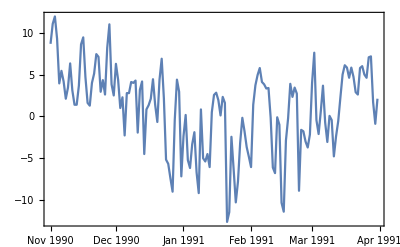
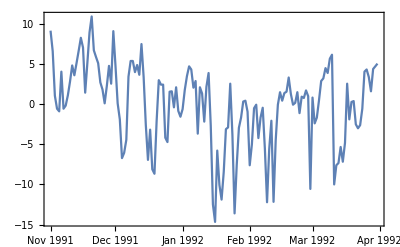
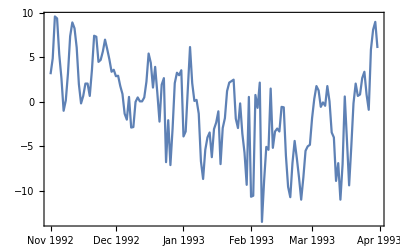
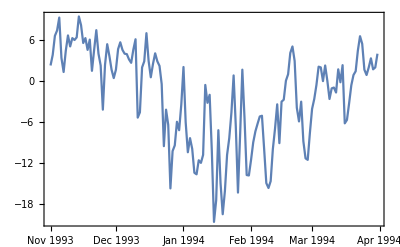
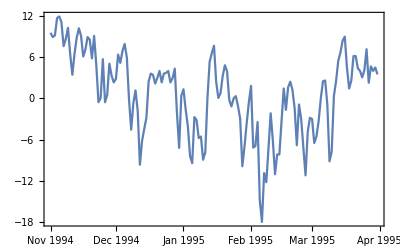
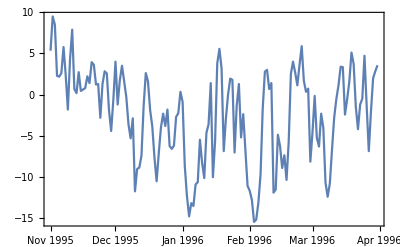
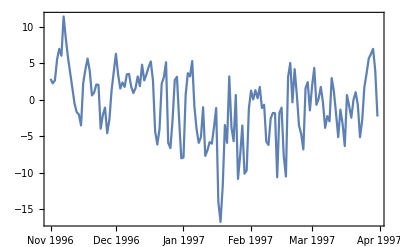
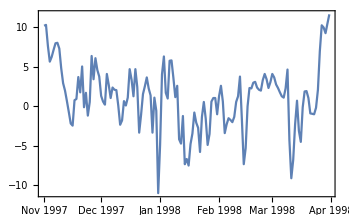

```mathematica
Table[DateListPlot[WeatherData["Toronto", "MeanTemperature", {{year, 11, 1}, {year+1, 3, 31}, "Day"}], Joined->True],{year, 1990, 2018}]
```

```mathematica
t = WeatherData["Toronto", "MeanTemperature", {{2000, 1, 1},{2019, 1, 1}, "Year"}] ;
t // FullForm
```

TemporalData[TimeSeries,List[List[StructuredArray[QuantityArray,List[20],StructuredArray`StructuredData[QuantityArray,List[8.31,9.38,9.53,7.78,5.75,7.38,10.49,9.76,9.28,9.12,10.58,10.11,11.32,9.46,8.51,9.33,10.66,9.8,9.6,1.17],"DegreesCelsius",List[List[1]]]]],List[TemporalData`DateSpecification[List[2000,1,1,0,0,0.],List[2019,1,1,0,0,0.],List[1,"Year"]]],1,List["Continuous",1],List["Discrete",1],1,List[Rule[ValueDimensions,1],Rule[DateFunction,Automatic],Rule[ResamplingMethod,List["Interpolation",Rule[InterpolationOrder,1]]]]],True,12.]

```mathematica
CityData["Toronto","Coordinates"]
```

{43.65,-79.38}

```mathematica
Part[t,2][[1]][[1]][[1]] [[1]]
```

-0.28

```mathematica
{{"Humidity"}, {"Temperature"}}

"MeanTemperature"
"MeanHumidity"
```

```mathematica
(WeatherData["Toronto", "Temperature", {#, 1,1}] // Mean) &/@ Range[2000,2019,1]
```

{3.212 °C,-8.425 °C,-3.84348 °C,0.566667 °C,2.325 °C,1/24 (4 Missing[NotAvailable]+-310.1 °C),-2.89565 °C,6.95 °C,0.316667 °C,-9.78333 °C,0.370833 °C,9.12917 °C,4.61304 °C,-3.1 °C,-10.5917 °C,-5.0875 °C,-0.2625 °C,1.30455 °C,-13.5917 °C,1.155 °C}

```mathematica
WeatherData["Toronto", "Temperature", {#, 1,1}] &/@ {2005}
```

{TimeSeries[…]}